# Frobenius: joining and splitting group labels

The Frobenius condition says that three ways of joining and splitting labels give the same answer. We will see each term of that answer for the six permutations of three objects. The main calculation uses lists of group labels, not index contractions. Evaluate the cells in order in a fresh kernel. All definitions and saved outputs are here; no companion file is needed.

Source: smsa.pdf v7.7, §17.2, Frobenius algebras, (17.35)–(17.38) and (17.42). This is a pedagogical adaptation of Symmetri2025/frobenius_condition.nb; the original is preserved. The matching v7.7 TeX and equation labels were unavailable. We work over the complex numbers, write e_g for the notes' delta-function basis, and initially use coproduct scale c = 1. Section 6 restores the exact normalization in (17.38). These are rescalings of the notes' example, not proposed corrections.

## 1. A basis vector carries a group label

Let A==ℂ(S_3). There is one basis vector e_g for each permutation g. A general element is a complex linear combination of these six basis vectors. Multiplication joins two labels: μ(e_g⊗e_h)==e_(g h). The unit is the basis vector labelled by the identity permutation.

Represent a permutation by the images of 1, 2 and 3. Thus {2,1,3} swaps 1 and 2. Our product applies the right permutation first: p[[q]] lists p(q(1)), p(q(2)), p(q(3)). Ordering[p] is the inverse permutation. The short names below are only for displaying answers.

```mathematica
Clear[elements,identity,product,inverse,names,name,split];elements=Permutations[{1,2,3}];identity={1,2,3};product[p_,q_]:=p⟦q⟧;inverse[p_]:=Ordering[p];names={"1","(23)","(12)","(123)","(132)","(13)"};name[p_]:=names⟦First[FirstPosition[elements,p]]⟧;Transpose[{elements,names}]
```

({1,2,3} | 1
{1,3,2} | (23)
{2,1,3} | (12)
{2,3,1} | (123)
{3,1,2} | (132)
{3,2,1} | (13))

Choose two swaps that do not commute. Predict the two products by following each of the three objects, before evaluating this cell.

```mathematica
g={2,1,3};h={1,3,2};{name[g],name[h],name[product[g,h]],name[product[h,g]]}
```

{(12),(23),(123),(132)}

The products are (123) and (132). Keeping their order is essential: our example is noncommutative. The Frobenius condition will hold anyway.

## 2. Splitting means listing every factorization

At scale c = 1, define Δ[e_g]=∑_(a b=g) e_a⊗e_b. This notation means one term for each ordered pair (a,b) with ab = g, each with coefficient one. It is a sum of basis tensors, not a random choice of a factorization.

We can list those pairs without solving equations: for every group element k take (gk, k inverse). Their product is g. Conversely, any factorization ab = g appears once, by choosing k==b^-1. Hence there are exactly six terms.

```mathematica
split[p_]:=Table[{product[p,k],inverse[k]},{k,elements}];(name/@#1&)/@split[g]
```

((12) | 1
(123) | (23)
1 | (12)
(23) | (132)
(13) | (123)
(132) | (13))

```mathematica
Association["Exactly six distinct terms"->Length[DeleteDuplicates[split[g]]]==6,"Every displayed pair multiplies to g"->AllTrue[split[g],product@@#1==g&]]
```

<|Exactly six distinct terms→True,Every displayed pair multiplies to g→True|>

For the identity label the six terms are the inverse pairs: Δ[e_1]=∑_(k∈S_3) e_k⊗e_(k^-1). This will also explain the unit and counit in Section 6.

## 3. Three routes, with every term visible

The two Frobenius equalities (17.35)–(17.36) can be written together as (id⊗μ)∘(Δ⊗id)==Δ∘μ==(μ⊗id)∘(id⊗Δ). Each route has two inputs and two outputs. Read composition from right to left.

The three diagrams show the same routes. Read every wire upward: the two labels enter at the bottom and the two output labels leave at the top. The blue nodes mark the operation performed at that height.

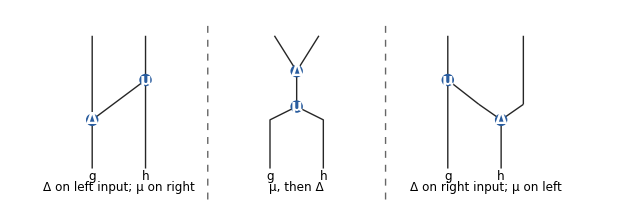

On the input labelled (g,h), join then split lists factorizations of gh. Split h first gives pairs (a,b) with ab = h; joining g to the left label changes each to (ga,b). Split g first gives pairs (a,b) with ab = g; joining h to the right label changes each to (a,bh). These are the only operations in the next cell.

```mathematica
joinThenSplit[p_,q_]:=split[product[p,q]];splitRightThenJoin[p_,q_]:=({product[p,#1⟦1⟧],#1⟦2⟧}&)/@split[q];splitLeftThenJoin[p_,q_]:=({#1⟦1⟧,product[#1⟦2⟧,q]}&)/@split[p];Transpose[{(name/@#1&)/@joinThenSplit[g,h],(name/@#1&)/@splitRightThenJoin[g,h],(name/@#1&)/@splitLeftThenJoin[g,h]}]
```

({(123),1} | {(123),1} | {(12),(23)}
{(12),(23)} | {(12),(23)} | {(123),1}
{(13),(12)} | {(13),(12)} | {1,(123)}
{(132),(132)} | {(132),(132)} | {(23),(13)}
{1,(123)} | {1,(123)} | {(13),(12)}
{(23),(13)} | {(23),(13)} | {(132),(132)})

Rows need not match: each route may list the terms in a different order. Addition of tensors allows reordering. Sorting the lists compares the same basis terms with the same multiplicities; it does not commute the two labels within any pair.

```mathematica
{Sort[joinThenSplit[g,h]]==Sort[splitRightThenJoin[g,h]],Sort[joinThenSplit[g,h]]==Sort[splitLeftThenJoin[g,h]]}
```

{True,True}

Both answers are True. We have checked one noncommuting input pair. The reason it works for every pair is more informative than the computation.

## 4. Why the condition holds for every finite group

The first route lists all (u,v) with uv = gh. In the second route, (a,b) becomes (ga,b), and b (a g)==g (a b)==g h. Conversely, from any (u,v) with uv = gh, recover the unique input labels a==u g^-1∧b==v, whose product is h. Thus the second route lists every factorization exactly once.

In the third route, (a,b) becomes (a,bh), with a (b h)==h (a b)==g h. The inverse correspondence has labels a==u∧b==v h^-1. Again there is neither a missing term nor an extra term. All three sums therefore agree for every finite group, without assuming commutativity.

Each map is linear, so equality on all basis inputs proves equality on every element of A tensor A, including superpositions. The next cell verifies the 36 basis inputs for S3; the bijection above is the general proof.

```mathematica
basisChecks=Flatten[Table[Sort[joinThenSplit[p,q]]==Sort[splitRightThenJoin[p,q]]&&Sort[joinThenSplit[p,q]]==Sort[splitLeftThenJoin[p,q]],{p,elements},{q,elements}]];Association["Basis inputs tested"->Length[basisChecks],"Both Frobenius equalities hold"->And@@basisChecks]
```

<|Basis inputs tested→36,Both Frobenius equalities hold→True|>

## 5. Why simply copying the label is different

The group algebra also has the Hopf coproduct Δ_H(e_g)==e_g⊗e_g. This copies the group label into both slots. It is not the factorization coproduct used here. On our chosen input, joining then copying gives (gh,gh), whereas copying h then joining on the left gives (gh,h).

```mathematica
hopfJoinThenCopy={product[g,h],product[g,h]};hopfCopyThenJoin={product[g,h],h};Association["Join then copy"->name/@hopfJoinThenCopy,"Copy h then join on left"->name/@hopfCopyThenJoin,"Frobenius equality"->hopfJoinThenCopy==hopfCopyThenJoin]
```

<|Join then copy→{(123),(123)},Copy h then join on left→{(123),(23)},Frobenius equality→False|>

The False answer is the expected counterexample: these are two different basis tensors. It does not say the Hopf coproduct is invalid; it obeys a different compatibility with multiplication.

## 6. Counit and normalization: connect back to the notes

For any nonzero complex number c set Δ_c[e_g]=c∑_(a b=g) e_a⊗e_b and ε_c(e_g)==(δ_(1 g))/c. The symbol on the right is the Kronecker delta: one for the identity label and zero otherwise. The unit remains η(1)==e_1.

The counit removes one output: only the term with identity in that slot survives, and the factors c and 1/c cancel. This returns the original basis vector. Every Frobenius route contains one splitting, so rescaling it multiplies all three routes by the same c. Coassociativity contains two splittings on either side; both sides list each triple factorization once with coefficient c squared.

Joining after splitting returns the same label six times: (μ∘Δ_c)(e_g)==6 c e_g. Also ε_c(η(1))==1/c. More generally, replace six by the order of the finite group.

```mathematica
{{"Convention", "c", "Scalar in join after split", "Counit after unit"}, {"Initial teaching convention", 1, 6, 1}, {"Notes (17.38)", 6, 36, 1/6}, {"Special convention (17.42)", 1/6, 1, 6}}
```

(Initial teaching convention | 1 | 6 | 1
Notes (17.38) | 6 | 36 | 1/6
Special convention (17.42) | 1/6 | 1 | 6)

The notes use c = |G|, hence c = 6 for S3. That structure is Frobenius but is not special with the definition (17.42). Choosing c = 1/|G| makes joining after splitting the identity, and the counit after the unit equals dim(A) = |G|. Both special conditions then hold. This distinction is a change of normalization, not a contradiction in the notes.

## 7. Check your understanding

Before opening the optional matrix check: (a) Write all six inverse pairs in the splitting of the identity. (b) Explain why reordering the six terms is allowed but swapping the two slots is a different operation. (c) For a group of order N, choose c to make joining after splitting the identity. (d) Explain where the proof in Section 4 uses an inverse, and why commutativity is unnecessary.

Answers: (a) (1,1), ((23),(23)), ((12),(12)), ((123),(132)), ((132),(123)), ((13),(13)). (b) Addition is commutative, but tensor slots are ordered. (c) c = 1/N, with counit value N on the identity basis vector. (d) The inverse maps recover (g inverse times u,v) and (u,v times h inverse); associativity gives the product equalities.

The idea to retain is the bijection of factorizations. Matrix calculations below verify the same maps and all algebra/coalgebra axioms, and show a superposition explicitly. They are optional; no index-contraction machinery is needed to understand the proof.

## Optional matrix check: maps, axioms and a superposition

Matrices are built from the basis images already described. Each column is the output on one input basis vector. Tensor pairs follow Tuples[elements,2], so the second label changes fastest. We display dimensions and Boolean checks, not large arrays.

```mathematica
n=Length[elements];pairBasis=Tuples[elements,2];vector[p_]:=UnitVector[n,First[FirstPosition[elements,p]]];tensorVector[u_,v_]:=Flatten[KroneckerProduct[u,v]];mu=Transpose[Table[vector[product@@pair],{pair,pairBasis}]];deltaOne=Transpose[Table[Total[(tensorVector[vector[#1⟦1⟧],vector[#1⟦2⟧]]&)/@split[p]],{p,elements}]];unit=Transpose[{vector[identity]}];counitOne={vector[identity]};id=IdentityMatrix[n];Association["Multiplication dimensions"->Dimensions[mu],"Splitting dimensions"->Dimensions[deltaOne],"Unit dimensions"->Dimensions[unit],"Counit dimensions"->Dimensions[counitOne]]
```

<|Multiplication dimensions→{6,36},Splitting dimensions→{36,6},Unit dimensions→{6,1},Counit dimensions→{1,6}|>

The general nonzero scale remains symbolic. In the expressions below a dot composes linear maps and KroneckerProduct makes them act on separate tensor slots.

```mathematica
Clear[c];deltaC=c deltaOne;counitC=counitOne/c;routeJoin=deltaC.mu;routeRight=KroneckerProduct[mu,id].KroneckerProduct[id,deltaC];routeLeft=KroneckerProduct[id,mu].KroneckerProduct[deltaC,id];studentChecks=Association["Associativity"->mu.KroneckerProduct[mu,id]==mu.KroneckerProduct[id,mu],"Left unit"->mu.KroneckerProduct[unit,id]==id,"Right unit"->mu.KroneckerProduct[id,unit]==id,"Coassociativity"->KroneckerProduct[deltaC,id].deltaC==KroneckerProduct[id,deltaC].deltaC,"Left counit"->KroneckerProduct[counitC,id].deltaC==id,"Right counit"->KroneckerProduct[id,counitC].deltaC==id,"Frobenius: split on right"->routeJoin==routeRight,"Frobenius: split on left"->routeJoin==routeLeft,"Join after split is 6 c times identity"->mu.deltaC==6 c id,"Counit after unit is 1/c"->counitC.unit=={{1/c}},"Special at c=1/6"->(mu.deltaC/.c->1/6)==id&&(counitC.unit/.c->1/6)=={{6}}];studentChecks=FullSimplify[studentChecks,c∈Complexes&&c≠0];KeyValueMap[{#1,#2}&,studentChecks]
```

(Associativity | True
Left unit | True
Right unit | True
Coassociativity | True
Left counit | True
Right counit | True
Frobenius: split on right | True
Frobenius: split on left | True
Join after split is 6 c times identity | True
Counit after unit is 1/c | True
Special at c=1/6 | True)

A concrete superposition is x==(2 e_g+e_1)⊗(e_h-ⅈ e_1). At c = 1, compare all three outputs and list their nonzero coefficients. Linearity predicts that the answer is the sum of four splittings, with coefficients 1, -i, 2 and -2i.

```mathematica
x=tensorVector[vector[identity]+2 vector[g],vector[h]-ⅈ vector[identity]];y=deltaOne.mu.x;expected=deltaOne.vector[h]-ⅈ deltaOne.vector[identity]+2 deltaOne.vector[product[g,h]]-2 ⅈ deltaOne.vector[g];Association["All routes agree on the superposition"->y==(routeRight/.c->1).x&&y==(routeLeft/.c->1).x,"Four-term linear expansion agrees"->y==expected,"Nonzero output coefficients"->Count[y,Except[0]]]
```

<|All routes agree on the superposition→True,Four-term linear expansion agrees→True,Nonzero output coefficients→24|>

```mathematica
Select[MapThread[{name/@#1,#2}&,{pairBasis,y}],Last[#1]≠0&]
```

({1,1} | -ⅈ
{1,(23)} | 1
{1,(12)} | -2 ⅈ
{1,(123)} | 2
{(23),1} | 1
{(23),(23)} | -ⅈ
{(23),(132)} | -2 ⅈ
{(23),(13)} | 2
{(12),1} | -2 ⅈ
{(12),(23)} | 2
{(12),(12)} | -ⅈ
{(12),(123)} | 1
{(123),1} | 2
{(123),(23)} | -2 ⅈ
{(123),(132)} | -ⅈ
{(123),(13)} | 1
{(132),(12)} | 1
{(132),(123)} | -ⅈ
{(132),(132)} | 2
{(132),(13)} | -2 ⅈ
{(13),(12)} | 2
{(13),(123)} | -2 ⅈ
{(13),(132)} | 1
{(13),(13)} | -ⅈ)